Data Imported as "FlopperData"

Time Differential

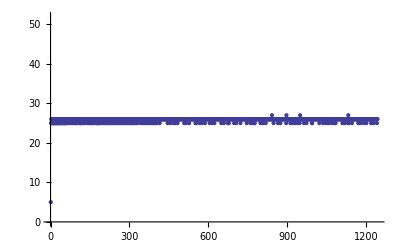

Time

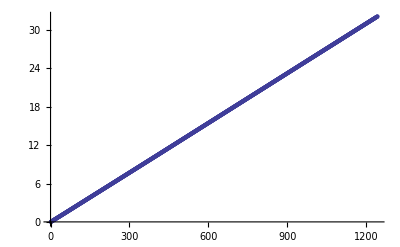

Angle

Data Imported as "FlopperData"

Time Differential

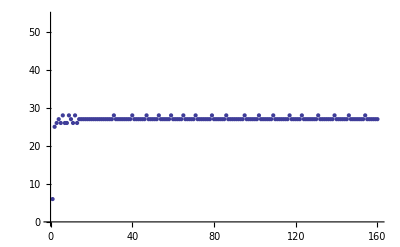

Time

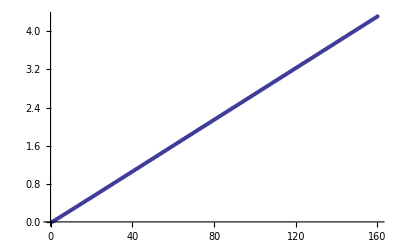

Angle

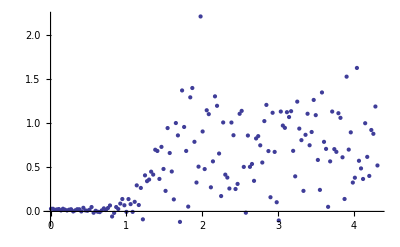

Angle Error

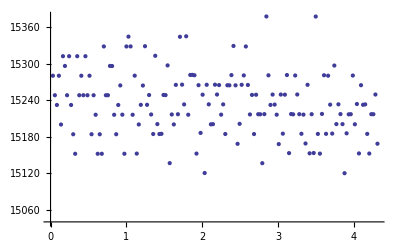

Integral

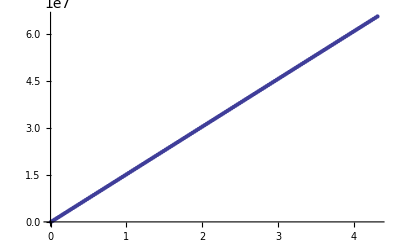

Derivative

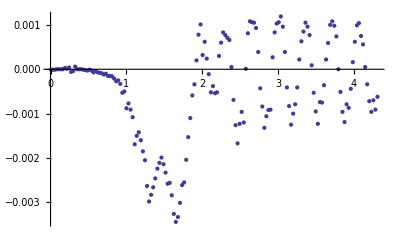

P Component

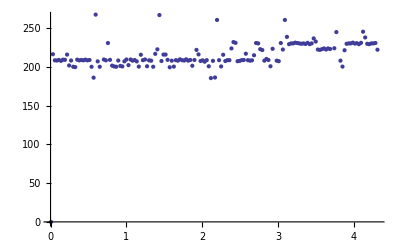

I Component

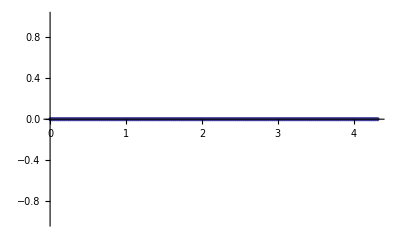

D Component

-Graphics-

Total Correction Value

-Graphics-

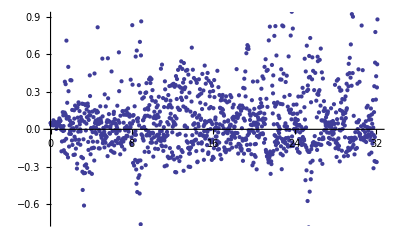

Angle Error

-Graphics-

Integral

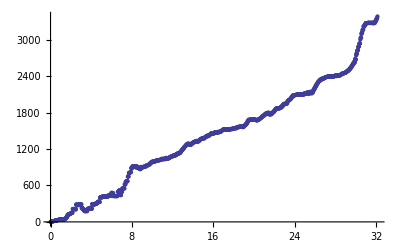

Derivative

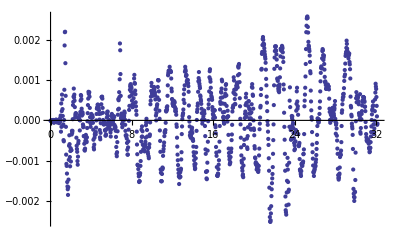

P Component

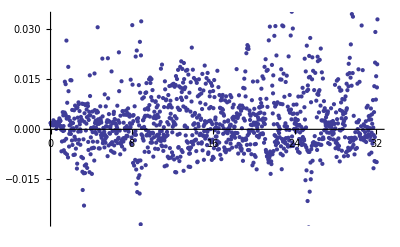

I Component

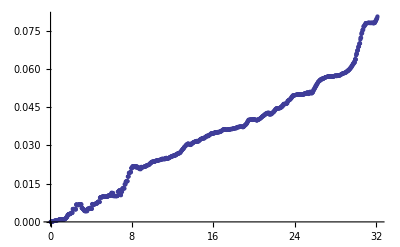

D Component

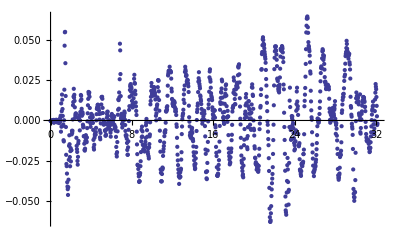

Total Correction Value

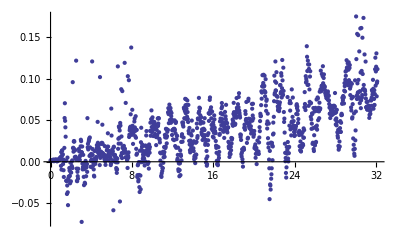

```mathematica
file = "C:\\Users\\Owner\\Desktop\\SensorData.csv";

FlopperData = Import[file];
FlopperData = Transpose[FlopperData];
Print["Data Imported as \"FlopperData\""];

dTime = FlopperData[[1]];
yAnglePV = FlopperData[[2]];
yAngleError = FlopperData[[3]];
integralYAngleError= FlopperData[[4]];
 yDerivative = FlopperData[[5]];
yP = FlopperData[[6]];
 yI= FlopperData[[7]];
yD = FlopperData[[8]];
yCorrection = FlopperData[[9]];
yProportionalGain = FlopperData[[10]];
yIntegralGain = FlopperData[[11]];
yDerivativeGain = FlopperData[[12]];

time = Accumulate[dTime]/1000;

Print["Time Differential"];
Print[ListPlot[dTime]];
Print["Time"];
Print[ListPlot[time]];
Print["Angle"];
Print[ListPlot[Table[{time[[i]],yAnglePV[[i]]},{i,Length[time]}]]];
Print["Angle Error"];
Print[ListPlot[Table[{time[[i]],yAngleError[[i]]},{i,Length[time]}]]];
Print["Integral"];
Print[ListPlot[Table[{time[[i]],integralYAngleError[[i]]},{i,Length[time]}]]];
Print["Derivative"];
Print[ListPlot[Table[{time[[i]],yDerivative[[i]]},{i,Length[time]}]]];
Print["P Component"];
Print[ListPlot[Table[{time[[i]],yP[[i]]},{i,Length[time]}]]];
Print["I Component"];
Print[ListPlot[Table[{time[[i]],yI[[i]]},{i,Length[time]}]]];
Print["D Component"];
Print[ListPlot[Table[{time[[i]],yD[[i]]},{i,Length[time]}]]];
Print["Total Correction Value"];
Print[ListPlot[Table[{time[[i]],yCorrection[[i]]},{i,Length[time]}]]];
```